### Functions

```mathematica
d=N[4/88]
```

0.0454545

```mathematica
GetCoord[n_]:=Module[{ans={},xy,i},
xy=RandomReal[TriangularDistribution[{-1,1},0],2];
While[√(xy[[1]]^2+xy[[2]]^2)>1-d,
xy=RandomReal[TriangularDistribution[{-1,1},0],2]];
AppendTo[ans,xy]; 
While[Length[ans]<n,
xy=RandomReal[TriangularDistribution[{-1,1},0],2];
While[!And[√(xy[[1]]^2+xy[[2]]^2)<1-d,Min[Table[√((xy[[1]]-ans[[i,1]])^2+(xy[[2]]-ans[[i,2]])^2),{i,Length[ans]}]]>2d],
xy=RandomReal[TriangularDistribution[{-1,1},0],2]];
AppendTo[ans,xy]];
Return[ans]]
```

```mathematica
PostColVel[o1_,v1_,o2_,v2_,e_]:=Module[{k,u1,u2},k=With[{t=o1-o2},t/Norm[t]];
u1=Re[v1+1/2 (1+e) (v2-v1).k k];u2=Re[v2-1/2 (1+e) (v2-v1).k k];
Return[Re[{u1,u2}]]]
```

```mathematica
tanLine[x_,x1_,y1_,r_]:=If[y1≠0,(r^2-x1 x)/y1,x1]
```

```mathematica
GetAngle[{x1_,y1_},{x2_,y2_}]:=Module[{tL1,tL2,ans,cf=1,a1,a2},
If[Or[And[y1==0,y2==0],And[x1==0,x2==0]],
ans=π/2,
tL1={{x2,tanLine[x2,x2,y2,1]},{x2-0.5,tanLine[x2-0.5,x2,y2,1]}};
tL2={{x2,tanLine[x2,x2,y2,1]},{x2+0.5,tanLine[x2+0.5,x2,y2,1]}};
a1=VectorAngle[{x1-x2,y1-y2},{-0.5,tanLine[x2-0.5,x2,y2,1]-tanLine[x2,x2,y2,1]}];
a2=VectorAngle[{x1-x2,y1-y2},{0.5,tanLine[x2+0.5,x2,y2,1]-tanLine[x2,x2,y2,1]}];
ans=Min[a1,a2];
(*Print[{x2,y2,ans,a1,a2,tL1,tL2}];*)
If[Or[And[x2>0,y2>0,ans==a1],And[x2>0,y2<0,ans==a2],And[x2<0,y2>0,ans==a1],And[x2<0,y2<0,ans==a2]],cf=-1]];
Return[{ans,cf}]]
```

```mathematica
GetTh[x_,y_]:=Module[{ans},ans=If[And[x==0,y==0],0,CoordinateTransformData["Cartesian"->"Polar", "Mapping",{x,y}][[2]]];If[ans<0,ans=ans+2π]; Return[Mod[ans,2π]]]
```

```mathematica
ReflectBoundaryTh[{x1_,y1_},{x2_,y2_}]:=Module[{ϕ,dx,dy,dr,DD,xp,yp,θ0,θn,xn,yn,l,v,xo,yo,A,tmp,cf},
If[y1==y2,
A={{-√(1-y1^2),y1},{√(1-y1^2),y1}},
dx=x2-x1;dy=y2-y1;dr=√(dx^2+dy^2);DD=x1 y2-x2 y1;
A={{(DD dy-Sign[dy]dx √(dr^2-DD^2))/dr^2,(-DD dx-Abs[dy] √(dr^2-DD^2))/dr^2},{(DD dy+Sign[dy]dx √(dr^2-DD^2))/dr^2,(-DD dx+Abs[dy] √(dr^2-DD^2))/dr^2}}];
{xp,yp}=If[EuclideanDistance[A[[1]],{x2,y2}]≤ EuclideanDistance[A[[2]],{x2,y2}],A[[1]],A[[2]]];
{ϕ,cf}=GetAngle[{x1,y1},{xp,yp}];
θ0=GetTh[xp,yp];
θn=If[Or[And[xp>0,yp<0,x1==xp],And[xp<0,yp>0,x1==xp]],Mod[θ0-2*ϕ,2π],Mod[θ0+2*cf*ϕ,2π]];xn=Cos[θn];yn=Sin[θn];
v=With[{t={xn,yn}-{xp,yp}},EuclideanDistance[{x1,y1},{x2,y2}]*t/Norm[t]];
{xo,yo}={xp,yp}+v;
(*Print[{{x1,y1},{x2,y2},{xp,yp},{ϕ,cf},{θ0/π,θn/π}}];*)
Return[{Re[{xo,yo}],v,{xp,yp,θ0,ϕ}}]]
```

```mathematica
MoveBeads[d_,o_,k_,e_,dt_,T_,nn_,rn_,mth_]:=Module[{ans={},p,ds,t=0,u,ut,n,u1,u2,i,j,pt,v,ii,jj,cm={},tcm},
n=Length[o];p=o;
AppendTo[ans,{p,Table[{0,0},{i,n}]}];
For[ii=0,ii<nn,
For[jj=1,jj≤ Length[mth],
v=k mth[[jj]];
u=Table[RandomVariate[UniformDistribution[{-rn,rn}]]+v,{i,n}];
While[t≤(jj+Length[mth] ii)T,
t=t+dt;
If[n>1,For[i=1,i≤ n,
For[j=i+1,j≤ n,
ds=EuclideanDistance[p[[i]],p[[j]]];
If[And[ds≤1.5 d,EuclideanDistance[p[[i]]+u[[i]],p[[j]]+u[[j]]]< EuclideanDistance[p[[i]]-u[[i]],p[[j]]-u[[j]]]],
{u1,u2}=PostColVel[p[[i]],u[[i]],p[[j]],u[[j]],1];
u[[i]]=u1;u[[j]]=u2;p[[i]]=p[[i]]+u[[i]]*dt;p[[j]]=p[[j]]+u[[j]]*dt];
j++];
i++]];
For[i=1,i≤ n,
If[Norm[p[[i]]+u[[i]]*dt]>1,
{pt,ut,tcm}=ReflectBoundaryTh[p[[i]],p[[i]]+u[[i]]*dt];
If[EuclideanDistance[{0,0},{tcm[[1]],tcm[[2]]}]≥ 0.95,AppendTo[cm,tcm]];
u[[i]]=ut/dt;p[[i]]=pt,
p[[i]]=p[[i]]+u[[i]]*dt];
i++];
AppendTo[ans,{p,u}];u=e*u];
jj++];
ii++];
Return[{Transpose[ans][[1]],cm}]]
```

### Initial positions of glass beds

```mathematica
oo={{-0.07867134919450325,-0.31790901427786933},{0.26456745197511,0.6072738306590939},{-0.4964990870730597,-0.4038900955678577},{0.046812208483353546,-0.4897209874258863},{0.2169529303099651,0.4128343505177541},{-0.40584927594449893,0.08925193508389007},{-0.3100250530226616,-0.19636086767426697},{0.34233439096597973,0.15667818243896625},{0.024095166267581458,-0.2482418307564611},{0.44638652054763783,-0.5489065476360848},{0.46449120045069536,-0.6850874648215166},{-0.444406517305,-0.1001252420044616},{0.13052900809446322,-0.7362018003786683},{-0.1771125536032394,-0.2897314831329256},{0.23736492168235235,-0.1560944096326391},{-0.24834627261324305,0.12643758925990967},{-0.05045691249025275,0.5407861467201407},{0.4598893338870562,-0.17530527718243616},{-0.6791775982392652,0.15492424417170358},{-0.03874495093143904,0.1702284472279727},{-0.3356646541894315,-0.09096973591554525},{-0.3961106693075016,0.7880131381365818},{0.2969822896083256,-0.611660648118209},{-0.06251786421687244,-0.11682443392812414},{-0.14001257890650032,0.46637776329148295}};
```

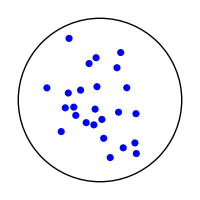

```mathematica
Show[Graphics[Circle[{0,0},1+d]],Table[Graphics[{Blue,Disk[oo[[i]],d]}],{i,Length[oo]}],ImageSize->200]
```

### Set up

Time step

```mathematica
dt=0.01;
```

### L-shape: n beads & nn loops

```mathematica
mth={{0,1},{1,0},{-1,0},{0,-1}};
```

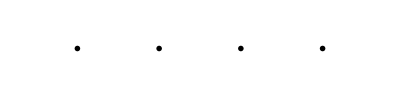

```mathematica
GraphicsRow[Table[Graphics[{Arrowheads[0.15],Arrow[{{0,0},mth[[i]]}]},ImageSize->75,AspectRatio->1],{i,Length[mth]}]]
```

```mathematica
n=10;
```

```mathematica
o=oo[[;;n]];
```

```mathematica
nn=5;
```

```mathematica
{mv,cm}=MoveBeads[d,o,3,0.99,dt,1,nn,0,mth];
```

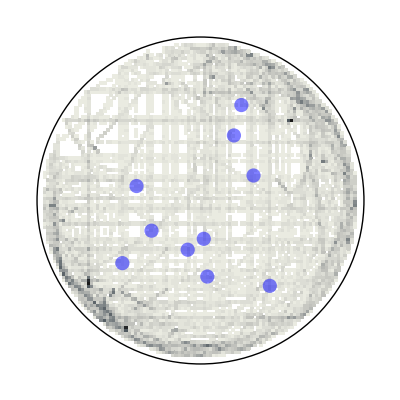

```mathematica
Show[Graphics[Circle[{0,0},1+d]],DensityHistogram[Flatten[mv,1],100,ColorFunction->(ColorData["GrayTones"][1-#]&)],Table[Graphics[{Blue,Opacity[0.5],Disk[o[[i]],d]}],{i,Length[o]}],AspectRatio->1]
```

### UD: n beads & nn loops

```mathematica
mth={{0,1},{0,-1}};
```

```mathematica
GraphicsRow[Table[Graphics[{Arrowheads[0.15],Arrow[{{0,0},mth[[i]]}]},ImageSize->75,AspectRatio->1],{i,Length[mth]}]]
```

-Graphics-

```mathematica
n=10;
```

```mathematica
o=oo[[;;n]];
```

```mathematica
nn=5;
```

```mathematica
{mv,cm}=MoveBeads[d,o,3,0.99,dt,1,nn,0,mth];
```

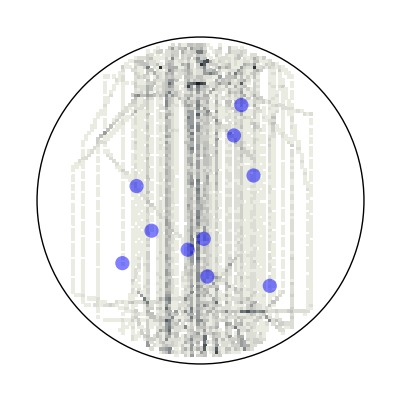

```mathematica
Show[Graphics[Circle[{0,0},1+d]],DensityHistogram[Flatten[mv,1],100,ColorFunction->(ColorData["GrayTones"][1-#]&)],Table[Graphics[{Blue,Opacity[0.5],Disk[o[[i]],d]}],{i,Length[o]}],AspectRatio->1]
```

### HG: n beads & nn loops

```mathematica
mth={{1,1}/√2,{-1,0},{1,-1}/√2,{-1,0}};
```

```mathematica
GraphicsRow[Table[Graphics[{Arrowheads[0.15],Arrow[{{0,0},mth[[i]]}]},ImageSize->75,AspectRatio->1],{i,Length[mth]}]]
```

-Graphics-

```mathematica
n=10;
```

```mathematica
o=oo[[;;n]];
```

```mathematica
nn=5;
```

```mathematica
{mv,cm}=MoveBeads[d,o,3,0.99,dt,1,nn,0,mth];
```

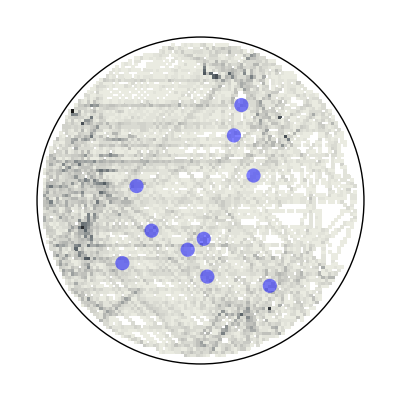

```mathematica
Show[Graphics[Circle[{0,0},1+d]],DensityHistogram[Flatten[mv,1],100,ColorFunction->(ColorData["GrayTones"][1-#]&)],Table[Graphics[{Blue,Opacity[0.5],Disk[o[[i]],d]}],{i,Length[o]}],AspectRatio->1]
```